```mathematica
X[J_,μ_]:= 1/2(J+μ);
B[J_]:= Exp[-J];
```

```mathematica
λp[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]+√((Sinh[X[J,μ]])^2+B[J]));
λm[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]-√((Sinh[X[J,μ]])^2+B[J]));
```

```mathematica
vm[J_,μ_]:= Exp[-μ/2](λm[J,μ]-1);
```

```mathematica
ϕav[J_,μ_,Nm_]:=(λp[J,μ]^Nm+λm[J,μ]^Nm vm[J,μ]^2)/((λp[J,μ]^Nm+λm[J,μ]^Nm)(1+vm[J,μ]^2));
N[ϕav[1,-2,12]]
ϕrav[J_,μ_,Nm_]:= 1/Nm Sum[ϕav[J,μ,Nm],{i,1,Nm}];
N[ϕrav[1,-2,100]]^2
```

0.174168

0.0303344

```mathematica
ξ[J_,μ_]:=Log[λp[J,μ]/λm[J,μ]]^-1
```

```mathematica
ϕcor[J_,μ_,Nm_,r_]:= (λp[J,μ]^Nm(1+Exp[-r/ξ[J,μ]] vm[J,μ]^2)+λm[J,μ]^Nm(Exp[r/ξ[J,μ]] vm[J,μ]^2+vm[J,μ]^4))/((λp[J,μ]^Nm+λm[J,μ]^Nm)(1+vm[J,μ]^2)^2);
```

```mathematica
ϕav2[J_,μ_,Nm_]:= 1/Nm^2 Sum[ϕcor[J,μ,Nm,r],{i,1,Nm},{r,1,Nm}] ;
N[ϕav2[2,-2,100]]
```

0.256796

```mathematica
var[J_,μ_,Nm_]:= ϕav2[J,μ,Nm]-ϕrav[J,μ,Nm]^2;
N[var[1,-1,200]]
```

0.0020609

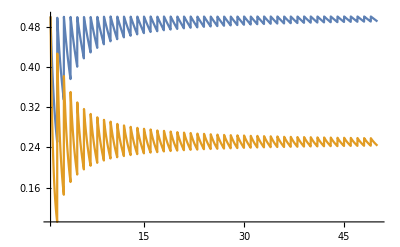

```mathematica
Plot[{ϕrav[1,-1,Nm],ϕav2[1,-1,Nm]},{Nm,1,50}]
```

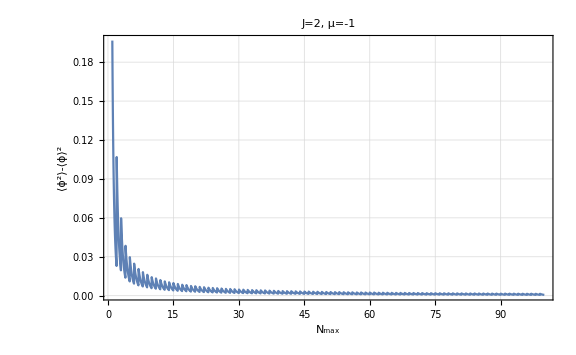

```mathematica
Plot[{var[2,-1,Nm]},{Nm,1,100}, PlotRange->Full, ImageSize->Large, Frame->True,GridLines->Automatic, FrameLabel->{"N_max","⟨ϕ^2⟩-⟨ϕ⟩^2"}, PlotLabel->"J=2, μ=-1", LabelStyle->{GrayLevel[0],12}]
```